```mathematica
trans:=(r - r a  Exp[I ϕ1])/(1-r^2   a  Exp[I ϕ1])
```

```mathematica
n:=3.45;
R1:=10 10^(-6);
d:= 2 Pi R1
λ:=1550 10^(-9); (* resonant wavelrngth *)
Q1:=1×10^5;
h := 1(* 0 for passive 1 for active*)
g := 140.01
α:=(2 Pi n)/(λ  Q1) (*139.85*)
a:= Exp[g d/2]
t:=√(1-r^2)
r:= 0.98
```

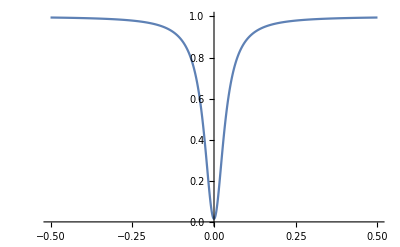

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
transdata:=Table[{ϕ1,Abs[trans]^2},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->{0,1}]
```

```mathematica
ϕ := Pi + ϕ1  + 2ArcTan[(r a  Sin[ϕ1])/(r-r a Cos[ϕ1])]
```

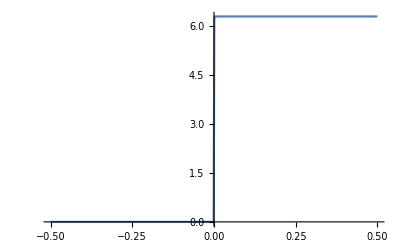

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
phasedata:=Table[{ϕ1,ϕ},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[phasedata,PlotRange->All]
```

```mathematica
Imag1 := ComplexExpand[Im[trans]]
Real1 := ComplexExpand[Re[trans]]
```

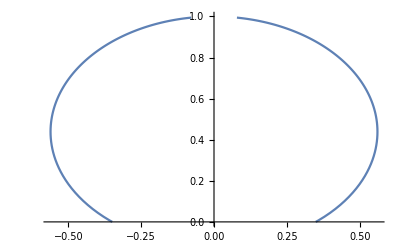

```mathematica
ImRedata:=Table[{Imag1,Real1},{ϕ1,-0.5, 0.5, 0.001}]
ListLinePlot[ImRedata,PlotRange->{0,1}]
```